```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSS`"];
```

## Functions that generate lists of integer "clues", and function to ID sessie network

### Explanations

MaxStateLengthPositions, LeastUsedRulePositions, DistanceTally, DistanceLastPositions

#### MaxStateLengthPositions: positions in "Evolution" where a new maximum state string length is reached for the first time

#### LeastUsedRulePositions: positions where the least-used rule was used

#### Note: both of these functions call a filtering function, MergeIntervalsByRulesUsed, which verifies that the same rules are used in each interval between positions in the list, and may discard unimportant positions.

#### DistanceLastPositions: a list containing, for each positive integer n, the position of the last nodes that is n steps from origin on the undirected graph of "Net".

Note: these first three provide lists of numbers based sessie events / network nodes, so as soon as a "Verdict" has been assigned, the CheckDimensions summaries can be used by GuessDimension and TestForUnusedRules.

#### DistanceTally: number of nodes in the undirected graph of "Net" that are no more than 1, 2, 3, ... steps from origin. (SSSAnimate[sss, VertexLabels → "VertexWeight"] gives a related, helpful visualization.)

#### CheckDimensions: accepts a list of "significant" positive integers, returns {"1D"|"2D"|...|"exp", n, {k, delay, matchlen, match}, dt}, indicating an n-dimensional or exponential network. Pattern detection required k-averaging, and a delay before the pattern was established and a difference or ratio match of length matchlen was detected. The difference table dt is provided for human inspection, but in theory it (but not the network) could be summarized as {n, dt⟦All, delay;;delay+k⟧} or {"exp", dt⟦All, delay;;delay+k⟧}, respectively. (In fact, only the first element of each row is needed, until the final row.) It is not currently clear whether k and match have any useful meaning in the exponential summary, but both can be reconstructed from the difference table summary. The function GuessDimension collects IDs ("1D", "2D", etc.) returned for any of the 4 significant number generator functions, and considers matchlen as a measure of reliability.

#### GuessDimension: with appropriate checks, tries all 4 approximative tests by applying CheckDimensions to the lists described above. Sessie is auto-extended to try to reach agreement. Changes "Verdict" if the combined matchlen values returned indicate satisfactory reliability.

#### TestForUnusedRules: decides whether to skip this case, and whether a long-jump is possible, once the sessie or the net has been identified (as "Repeating" or otherwise by GuessDimension).

#### Possible issues & notes:

(1) If dt⟦1,1⟧ == j ≠ 1, there was some initial stuff before the pattern set in.

Solution: If the numbers were provided by either MaxStateLengthPositions or LeastUsedRulePositions, toss out the first j-1 steps of the sessie to generate a network with a difference table in which the first j-1 columns are dropped, and the first row entries are all reduced by subtracting j-1.  If the numbers were produced from the "Net", it's unclear how much of the sessie state strings should be skipped.

(2) Once reliable ID has been made, call TestForUnusedRules to decide whether to skip this case, and whether a long-jump is possible:  affects acceleration.  Later call ImproveInitialState (not yet written), to discard initial or final tagged cells unchanged by the evolution:  only affects sessie display, not the network.  Think carefully about unchanged interior tagged cells:  removing an inert cell might allow a different evolution.

(*) Once we have a network summary...:  Depending on the initial state string, a different network summary might be generated:  how to recognize their equivalence?

Possible solution: Make k alternative summaries, treating by dropping 0, 1, …, k-1 states [as in (1)], sort them (perhaps by last row, then next-to-last, etc.), treat as "canonical" the first in the sorted list.

### Code

```mathematica
LeastUsedRulePositions[sss_Association /; KeyExistsQ[sss,"RulesUsed"]] := Module[{ru=sss["RulesUsed"],len,ruletally,least},
len=Length[ru];
ruletally=Tally[ru⟦Round[.1len];;len⟧];      (* skip 10% -- ARBITRARY! -- of rules used, tally the rest *)
least=First@First@SortBy[ruletally,Last];  (* identify the least used rule *)
MergeIntervalsByRulesUsed[Flatten@Position[ru,least],ru]  (* find its occurrences anywhere, merge intervals -- IS THIS NECESSARY?! -- and return *) 
];
```

```mathematica
LeastUsedRulePositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the least-used rule was applied (least-used in the last 90% of the evolution).  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MaxStateLengthPositions[sss_Association /; KeyExistsQ[sss,"Evolution"]]:=Module[{currmaxlenstringlen,strlens,strt,evollen,evol=sss["Evolution"],b=Boole[sss["Verdict"]==="Repeating"]},
evollen=Length[evol];
strlens=StringLength /@ evol;
currmaxlenstringlen=Min[strlens];
strt=First@First[Position[strlens,currmaxlenstringlen,1]];
Most@
MergeIntervalsByRulesUsed[
Last@Last@Reap[
Do[
If[StringLength[evol⟦n⟧]>currmaxlenstringlen-b,(* if repeating, "≥" *)
Sow[n]; currmaxlenstringlen=StringLength[evol⟦n⟧]
],
{n,strt,evollen}]
],
sss["RulesUsed"]
]
];
```

```mathematica
MaxStateLengthPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the sessie state string reached a new maximum length, starting with the minimum length string -- which hopefully eliminates some initial non-pattern stuff.  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MergeIntervalsByRulesUsed[l0_List,ru_List] := Module[{l=l0,n=Length[l0],rulesused1,rulesused2},
(* Expects a list of interesting integers (l0, defining intervals) and the "RulesUsed" list of some SSS.  Merges any intervals in which fewer different rules were used than in neighboring intervals.
Returns the resulting list, which should be more meaningful than the original one. Give up if length ≤ 2 *) 
While[n>2,
rulesused1=Union[ru⟦l⟦n-2⟧;;l⟦n-1⟧-1⟧];
rulesused2=Union[ru⟦l⟦n-1⟧;;l⟦n⟧-1⟧];
(* If[$debug,Print["rules used:", rulesused1,", ",rulesused2]]; *)
Which[
rulesused1==rulesused2, n--,
SubsetQ[rulesused1,rulesused2], l=Drop[l,{n}];n=Length[l],
SubsetQ[rulesused2,rulesused1], l=Drop[l,{n-2}];n=Length[l],
True,l=Drop[l,{n-1}];n=Length[l]
]
];
l]
```

```mathematica
Clear[ReliableDistances];ReliableDistances[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := Module[{len,net=sss["Net"],odr,z,eins,pos,distances,maxdistance},
If[Length[net]==0,Return[{}]];  (* no network, no distances! *)
eins=Min[Flatten[net/.Rule->List]];
If[$debug,Print["smallest node in net: ",eins]];
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees, after skipping first 10% *)
len=Length[sss["OutDegreeRemaining"]];
odr=ReplacePart[sss["OutDegreeRemaining"],_?(#<.1len&)->∞];  (* set first 10% = ∞, these will be ignored *)
If[$debug,Print["OutDegreeRemaining (massaged): ", odr]];
z = Min[odr];  
If[$debug,Print["treating as zero (in odr): ", z]];
(* for our purposes, z will be treated as 0, nodes that are as complete as possible have outdegree remaining = z *)
If[$debug,Print["using \"OutDegreeRemaining\" to find end of reliable data: ",
(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>{{g},{f},{h}})]];
pos=(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>Length[{g,f}]+Flatten@Position[{h},_?(#≠0&)]);If[$debug,Print["Position of first untrustworthy node: ", pos]]; 
(* distances = sss["Distance"]; *)   (* now using undirected graph distances... *)
distances = GraphDistance[UndirectedGraph[sss["Net"]],eins];
If[$debug,Print["distances (uncut): ",distances]];
maxdistance=Min[distances⟦pos⟧];
If[$debug,Print["last distance we'll trust: ", maxdistance]];
distances /. _?(#>maxdistance&)->-1  (* replace unreliable distances by -1 *)
];
```

```mathematica
DistanceLastPositions[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := 
(* find the position of the last node with (reliable) distance 1, 2, ... *)
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
MergeIntervalsByRulesUsed[
Last[Last[Position[rd,#,{1}]]]& /@ Range[Max[Complement[rd,{∞}]]],
sss["RulesUsed"]
]
]
];
DistanceLastPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions {n_1, n_2, …, n_k} in its causal network, each of which is the last node at the indicated distance from the origin.  Thus n_1 is the node of maximum index which is 1 step away, n_2 the largest that is 2 steps away, etc. But only the final 90% of the network is considered. This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
DistanceTally[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] :=   
(* tally reliable distances, sort, drop the unreliable (-1 & ∞) tally, keep numbers only *) 
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
Accumulate[Last /@ Rest@Sort@DeleteCases[Tally[rd],{∞,_}]]
]
];
DistanceTally::usage = "Takes sss, an already generated sessie object, and returns the list of how many nodes are 0 steps from the origin, how many 1 step away, how many 2 steps away, …. But only the final 90% of the network is considered.";
```

```mathematica
LongestPositiveSubsequence[l_List] := Module[{mx,spl},
spl=SplitBy[l/.ComplexInfinity->∞,0≤#<∞&];
mx=Max[Length/@spl];
First[Select[spl,Length[#]==mx&]]
]
```

```mathematica
Clear[RecognizeDifferenceRow];
RecognizeDifferenceRow[l_List] := Module[{len=Length[l],ptrn,dlay,mtch,mtchlen,k,rats},
For[k=1,k≤len/2,k++,  (* for each possible size moving average run k *)
ptrn=MovingAverage[l,k];
(* Print["ptrn: ",ptrn]; *)
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtchlen,mtch}=(ptrn/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_,{5,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b}); 
Return[{"dim",{k,dlay,mtchlen,mtch}}]  (* constant row found, needed k-averaging, after dlay, including a mtch of length mtchlen *)
];
Off[Divide::infy,Divide::indet];
rats=LongestPositiveSubsequence[Ratios[ptrn]];  (* try ratios instead *)
(* Print["rats: ",rats]; *)
If[MatchQ[rats,{Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 3 repeated positive ratios between *)
{dlay,mtchlen,mtch}=(rats/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_?(#>1&),{3,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b});
On[Divide::infy,Divide::indet];
Return[{"exp",{k,dlay,mtchlen,mtch}}] (* exponential, needed k-averaging, after dlay, including a mtch of length mtchlen *)
]
];
{}]  (* {} = failure, {"dim"|"exp", {k, dlay, (max) match length,(diff|ratio)mtch}} = success! *)
```

```mathematica
CheckDimension[l_List]:=Module[{diffsTable={l,Differences[l]},lastrow,ans,k,dlay,mtchlen,mtch},
While[Length[lastrow=Last[diffsTable]]≥5, (* stop when rows become too short *)
ans=RecognizeDifferenceRow[lastrow];  (* try to ID this row *)
If[Length[ans]>0, 
(* success, get details: k-averaging, after dlay, match of length mtchlen *)
{k,dlay,mtchlen,mtch}=ans⟦2⟧;
Return[{
Switch[ans⟦1⟧,
"exp","exp" (* <>ToString[Length[diffsTable]-1] *),
"dim",ToString[Length[diffsTable]-1]<>"D"
],
ans⟦2⟧,
Framed@Grid[diffsTable⟦All,dlay+1;;dlay+k⟧],Grid[diffsTable]}],
(* failure, add another row, try again *)
AppendTo[diffsTable,Differences[Last[diffsTable]]]
]
];
{"failed",Grid[diffsTable]}]
```

```mathematica
Clear[GuessDimension];
SetAttributes[GuessDimension,HoldFirst];
GuessDimension[sss0_] := Module[{len,sss,ans,anssum,vdct,chngd=False,RC},
(* may change the "Verdict" field of the SSS object passed as an argument *)
sss=Evaluate[sss0]; (* local copy to use *)
If[!KeyExistsQ[sss,"Evolution"],Return["Invalid input"]];
If[MatchQ[vdct=sss["Verdict"],"Repeating"|"Dead"], Return[vdct]];

len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];

While[len<5000 && anssum⟦1,-1⟧<10+5*Length[anssum],(* try for agreement *)
chngd=True;
sss=SSSEvolve[sss,len*Round[(10+5*Length[anssum]-anssum⟦1,-1⟧)/5]];  (* extend the sss evolution a bit, depending *)
len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];
];
vdct=If[Length[anssum]==1,anssum⟦1,1⟧ (* agree! *), anssum (* disagree *)];  
If[len<5000 , chngd=True; sss["Verdict"]=vdct]; (* trust it *)
If[chngd,sss0=sss]; (* update it if changed *)
Print[vdct];
ans
];
```

## Sessie Examples from NKS

#### p. 90

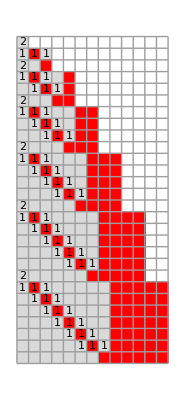


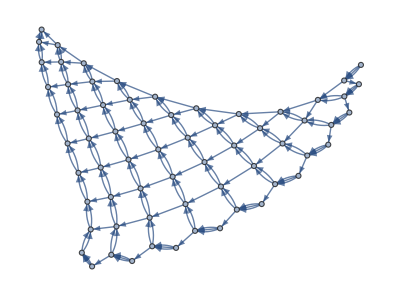
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss90=SSS[{"ABA"->"AAB","A"->"ABA"}, "A",75,SSSMax->28,NetMax->65,NetSize->{Automatic,300},SSSSize->{Automatic,220},VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True];
```

Use SSSInteractiveDisplay to try other options:

```mathematica
SSSInteractiveDisplay[sss90]
```

```mathematica
sss90["Evolution"]⟦1;;12⟧
```

{A,ABA,AAB,ABAAB,AABAB,AAABB,ABAAABB,AABAABB,AAABABB,AAAABBB,ABAAAABBB,AABAAABBB}

```mathematica
Sort[sss90["Net"]]⟦1;;15⟧
```

{1→2,1→2,1→2,2→3,2→5,3→4,3→4,3→4,4→5,4→5,4→6,5→8,5→9,6→7,6→7}

```mathematica
sss90["Net"]//Sort
```

{1→2,1→2,1→2,2→3,2→5,3→4,3→4,3→4,4→5,4→5,4→6,5→8,5→9,6→7,6→7,6→7,7→8,7→8,7→10,8→9,8→9,8→12,9→13,9→14,10→11,10→11,10→11,11→12,11→12,11→15,12→13,12→13,12→17,13→14,13→14,13→18,14→19,14→20,15→16,15→16,15→16,16→17,16→17,16→21,17→18,17→18,17→23,18→19,18→19,18→24,19→20,19→20,19→25,20→26,20→27,21→22,21→22,21→22,22→23,22→23,22→28,23→24,23→24,23→30,24→25,24→25,24→31,25→26,25→26,25→32,26→27,26→27,26→33,27→34,27→35,28→29,28→29,28→29,29→30,29→30,29→36,30→31,30→31,30→38,31→32,31→32,31→39,32→33,32→33,32→40,33→34,33→34,33→41,34→35,34→35,34→42,35→43,35→44,36→37,36→37,36→37,37→38,37→38,37→45,38→39,38→39,38→47,39→40,39→40,39→48,40→41,40→41,40→49,41→42,41→42,41→50,42→43,42→43,42→51,43→44,43→44,43→52,44→53,44→54,45→46,45→46,45→46,46→47,46→47,46→55,47→48,47→48,47→57,48→49,48→49,48→58,49→50,49→50,49→59,50→51,50→51,50→60,51→52,51→52,51→61,52→53,52→53,52→62,53→54,53→54,53→63,54→64,54→65,55→56,55→56,55→56,56→57,56→57,56→66,57→58,57→58,57→68,58→59,58→59,58→69,59→60,59→60,59→70,60→61,60→61,60→71,61→62,61→62,61→72,62→63,62→63,62→73,63→64,63→64,63→74,64→65,64→65,64→75,66→67,66→67,66→67,67→68,67→68,68→69,68→69,69→70,69→70,70→71,70→71,71→72,71→72,72→73,72→73,73→74,73→74,74→75,74→75}

#### p. 91a

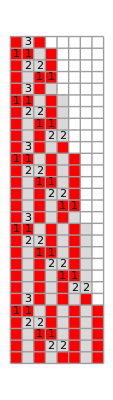
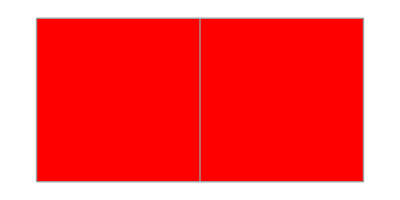


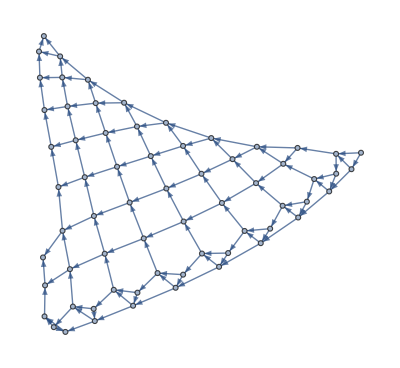
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss91a=SSS[{"BB"->"BA","AA"->"AB","A"->"BA"},"BAB",75,SSSMax->28,NetMax->65,NetSize->{Automatic,300},ImageSize->150,SSSSize->{Automatic,220},VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True];
```

#### p. 91b

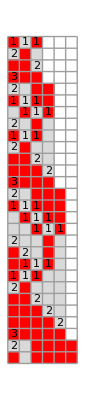
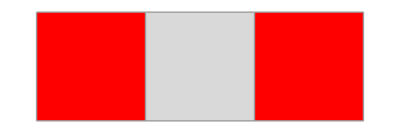

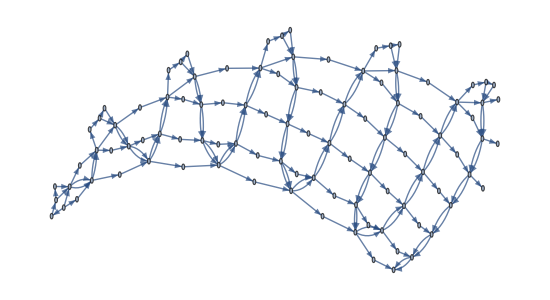
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss91b=SSS[{"BAB"->"ABA","A"->"B","B"->"AA"},"BAB",100,SSSMax->28,NetMax->100,NetSize->{550,300},SSSSize->{Automatic,220},VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True];
```

#### p. 91c

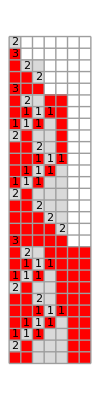
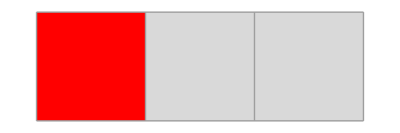
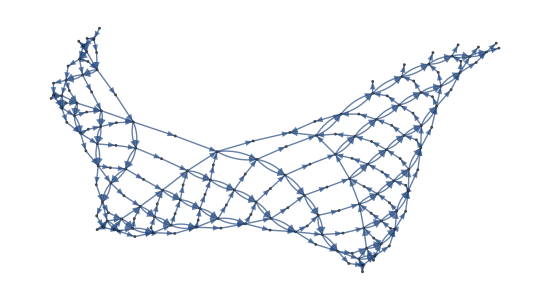
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss91c=SSS[{"BAB"->"ABA","A"->"B","B"->"BAA"},"A",200,SSSMax->28,NetMax->178,NetSize->{550,300},SSSSize->{Automatic,220},VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True];
```

#### p. 91d

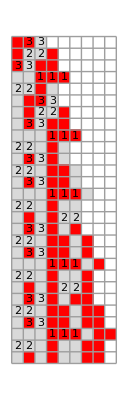
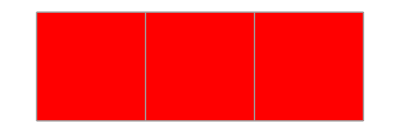
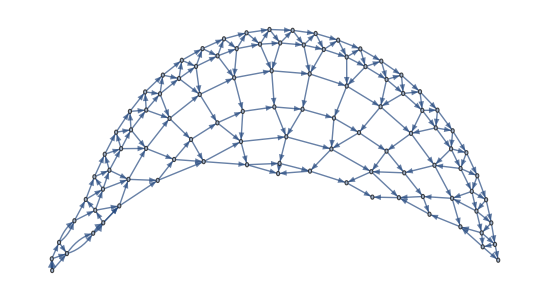
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss91d=SSS[{"BBB"->"BA","AA"->"AB","BA"->"AAB"},"BBA",100,SSSMax->28,NetMax->100,NetSize->{550,300},SSSSize->{Automatic,220},VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True];
```

#### p. 91e

This network makes me doubt any definition of dimension.  According to the number of nodes a certain distance from the origin, it has dimension 2.  But visually the network is becoming too dense for 2-d or indeed any dimension, along the “ruffled” edge.  How?  Of course, none of these are effects of future events on the “inner” edge, so maybe there’s no problem.

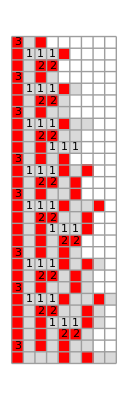
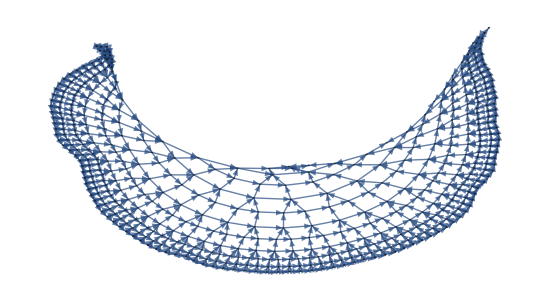
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss91e=SSS[{"AAA"->"AB","BB"->"BA","B"->"BAA"},"BAB",600,SSSMax->28,NetMax->500,NetSize->{550,300},SSSSize->{Automatic,220},VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True];
```

#### p. 91f

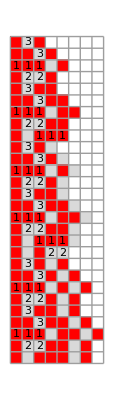
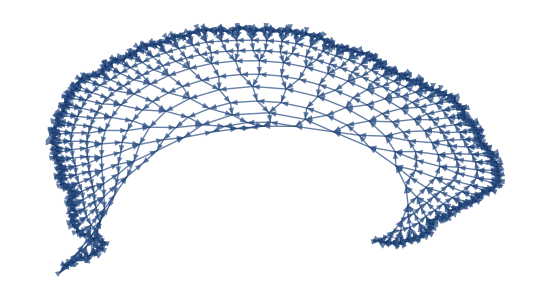
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss91f=SSS[{"BBB"->"BA","AA"->"AB","A"->"BA"},"BAB",800,SSSMax->28,NetMax->800,NetSize->{550,300},SSSSize->{Automatic,220},VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True];
```

#### p. 91g

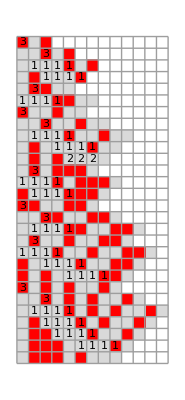
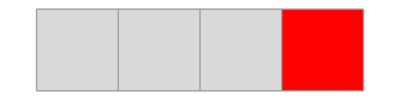
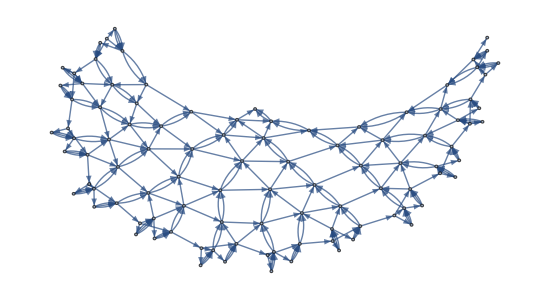
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss91g=SSS[{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},"BAB",100,SSSMax->28,NetMax->100,NetSize->{550,300},SSSSize->{Automatic,220},VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True];
```

#### p. 91h

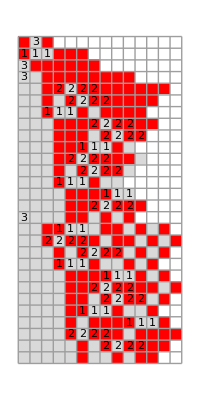
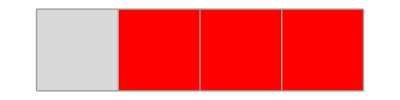
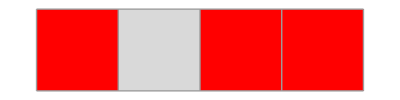
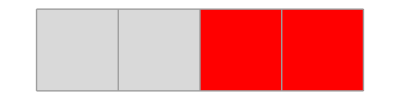
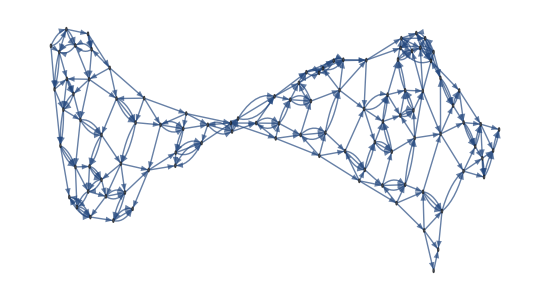
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss91h=SSS[{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"},"BAB",100,SSSMax->28,NetMax->100,NetSize->{550,300},SSSSize->{Automatic,220},VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True];
```

No clear pattern, extend the evolution:

```mathematica
sss91h=SSSEvolve[sss91h,3000];
```

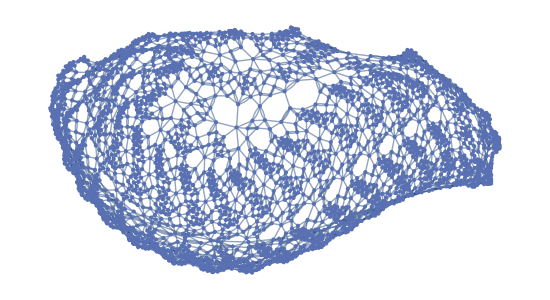
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss91h,SSSMax->28,NetSize->{550,300},SSSSize->{Automatic,220},VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False]
```

Still no clear pattern!  But it sure is interesting.

#### Start working on network identification....

```mathematica
IdentifyPseudorepeating
{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}
```

{{failed,1 | 3 | 6 | 10 | 15 | 21
2 | 3 | 4 | 5 | 6 | 
1 | 1 | 1 | 1 |  | 
0 | 0 | 0 |  |  | ,{Indeterminate,Indeterminate}},{failed,2 | 4 | 7 | 11 | 16 | 22
2 | 3 | 4 | 5 | 6 | 
1 | 1 | 1 | 1 |  | 
0 | 0 | 0 |  |  | ,{Indeterminate,Indeterminate}},{failed,
,{}},{failed,2 | 5 | 9 | 14 | 20
3 | 4 | 5 | 6 | 
1 | 1 | 1 |  | ,{1.,1.}}}

sssSummary: {}

distanceTallyAns: {{failed,1 | 2 | 4 | 7 | 11 | 16
1 | 2 | 3 | 4 | 5 | 
1 | 1 | 1 | 1 |  | 
0 | 0 | 0 |  |  | ,{Indeterminate,Indeterminate}},{2, riffling by ,1,: ,{1,1,1,1}}}

distanceTallySummary: {2}

No successful SSS tests

{True,2qq}

{2,{∞,∞}}

```mathematica
SSSEvolve[20]
IdentifyPseudorepeating
{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}
```

2

{{2,{1,∞},1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2,{2,∞},2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{failed,1
,{}},{2,{2,∞},2 | 5 | 9 | 14 | 20 | 27 | 35
3 | 4 | 5 | 6 | 7 | 8 | 
1 | 1 | 1 | 1 | 1 |  | }}

sssSummary: {{2,{1,∞}},{2,{2,∞}},{2,{2,∞}}}

distanceTallyAns: {{2,{1,∞},1 | 2 | 4 | 7 | 11 | 16 | 22 | 29
1 | 2 | 3 | 4 | 5 | 6 | 7 | 
1 | 1 | 1 | 1 | 1 | 1 |  | },{2, riffling by ,1,: ,{1,1,1,1,1,1}}}

distanceTallySummary: {2}

{True,{2,{1,∞}}}

{2,{∞,1}}

```mathematica
SSSEvolve[100]
IdentifyPseudorepeating
{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}
```

2

{{2,{1,∞},1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66 | 78 | 91 | 105 | 120 | 136
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2,{2,∞},2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56 | 67 | 79 | 92 | 106 | 121 | 137
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{failed,1
,{}},{2,{2,∞},2 | 5 | 9 | 14 | 20 | 27 | 35 | 44 | 54 | 65 | 77 | 90 | 104 | 119
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }}

sssSummary: {{2,{1,∞}},{2,{2,∞}},{2,{2,∞}}}

distanceTallyAns: {{2,{1,∞},1 | 2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56 | 67 | 79 | 92 | 106
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2, riffling by ,1,: ,{1,1,1,1,1,1,1,1,1,1,1,1,1}}}

distanceTallySummary: {2}

{True,{2,{1,∞}}}

{2,{∞,1}}

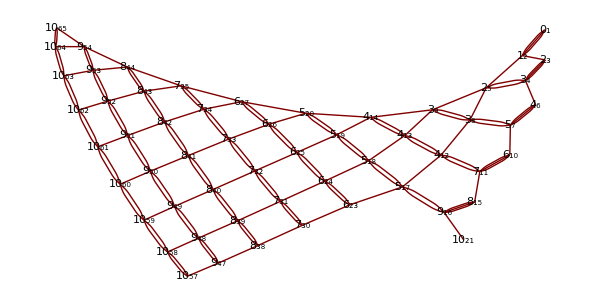

```mathematica
SSSDisplay[UseDistances->True,DistanceMax->10,NetMethod->{NoSSS,GraphPlot},NetSize->600]
```

```mathematica
SSSAnimateByDistance
```

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

{dim,2,2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56 | 67 | 79
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
$SSSDistance
```

{0,1,2,3,2,4,5,3,3,6,7,4,4,4,8,9,5,5,5,5,10,11,6,6,6,6,6,12,13,7,7,7,7,7,7,14,15,8,8,8,8,8,8,8,16,17,9,9,9,9,9,9,9,9,18,19,10,10,10,10,10,10,10,10,10,20,21,11,11,11,11,11,11,11,11,11,11,22,23,12}

```mathematica
checkDimension@MergeIntervals@DistanceLastPositions
```

{dim,2,2 | 5 | 9 | 14 | 20 | 27 | 35 | 44 | 54 | 65
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
checkDimension@DistanceTally
```

{dim,2,2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
checkDimension /@ MergeIntervals /@ MinRulePositions
```

{{dim,2,1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66 | 78
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }}

```mathematica
CommonestHistoryPositions
```

Insufficient data

{}

```mathematica
SSSEvolve[100]
```

Pseudorepeating

```mathematica
checkDimension@MergeIntervals@CommonestHistoryPositions
```

{dim,2,66 | 78 | 91 | 105 | 120 | 136 | 153 | 171
12 | 13 | 14 | 15 | 16 | 17 | 18 | 
1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
IdentifyPseudorepeating
```

{{2,{1,∞},1 | 5 | 10 | 16 | 23 | 31 | 40 | 50 | 61 | 73 | 86 | 100 | 115 | 131 | 148 | 166 | 185
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2,{2,∞},2 | 6 | 11 | 17 | 24 | 32 | 41 | 51 | 62 | 74 | 87 | 101 | 116 | 132 | 149 | 167 | 186
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{failed,
,{}},{2,{3,∞},3 | 6 | 11 | 17 | 24 | 32 | 41 | 51 | 62 | 74 | 87 | 101 | 116 | 132 | 149 | 167 | 186
3 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }}

sssSummary: {{2,{1,∞}},{2,{2,∞}},{2,{3,∞}}}

distanceTallyAns: {{2,{1,∞},1 | 3 | 6 | 10 | 16 | 23 | 31 | 40 | 50 | 61 | 73 | 86 | 100 | 115 | 131 | 148 | 166 | 185
2 | 3 | 4 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2, riffling by ,1,: ,{1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

distanceTallySummary: {2}

{True,{2,{1,∞}}}

```mathematica
SSSEvolve[500]
IdentifyPseudorepeating
{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}
```

2

{{2,{1,∞},1 | 5 | 10 | 16 | 23 | 31 | 40 | 50 | 61 | 73 | 86 | 100 | 115 | 131 | 148 | 166 | 185 | 205 | 226 | 248 | 271 | 295 | 320 | 346 | 373 | 401 | 430 | 460 | 491 | 523 | 556 | 590 | 625 | 661 | 698
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2,{2,∞},2 | 6 | 11 | 17 | 24 | 32 | 41 | 51 | 62 | 74 | 87 | 101 | 116 | 132 | 149 | 167 | 186 | 206 | 227 | 249 | 272 | 296 | 321 | 347 | 374 | 402 | 431 | 461 | 492 | 524 | 557 | 591 | 626 | 662 | 699
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2,{74,∞},74 | 101 | 132 | 167 | 206 | 249 | 296 | 347 | 402 | 461 | 524 | 591 | 662
27 | 31 | 35 | 39 | 43 | 47 | 51 | 55 | 59 | 63 | 67 | 71 | 
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 |  | },{2,{3,∞},3 | 6 | 11 | 17 | 24 | 32 | 41 | 51 | 62 | 74 | 87 | 101 | 116 | 132 | 149 | 167 | 186 | 206 | 227 | 249 | 272 | 296 | 321 | 347 | 374 | 402 | 431 | 461 | 492 | 524 | 557 | 591 | 626 | 662 | 699
3 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 
2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }}

sssSummary: {{2,{1,∞}},{2,{2,∞}},{2,{74,∞}},{2,{3,∞}}}

distanceTallyAns: {{2,{1,∞},1 | 3 | 6 | 10 | 16 | 23 | 31 | 40 | 50 | 61 | 73 | 86 | 100 | 115 | 131 | 148 | 166 | 185 | 205 | 226 | 248 | 271 | 295 | 320 | 346 | 373 | 401 | 430 | 460 | 491 | 523 | 556 | 590 | 625 | 661 | 698
2 | 3 | 4 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 
1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2, riffling by ,1,: ,{1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

distanceTallySummary: {2}

{True,{2,{1,∞}}}

{2,{∞,1}}

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

{dim,2,2 | 6 | 11 | 17 | 24 | 32 | 41 | 51 | 62 | 74 | 87 | 101 | 116 | 132 | 149 | 167 | 186
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
checkDimension@MergeIntervals@DistanceLastPositions
```

{dim,2,3 | 6 | 11 | 17 | 24 | 32 | 41 | 51 | 62 | 74 | 87 | 101 | 116 | 132 | 149 | 167 | 186
3 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
checkDimension@DistanceTally
```

{dim,2,3 | 6 | 10 | 16 | 23 | 31 | 40 | 50 | 61 | 73 | 86 | 100 | 115 | 131 | 148 | 166 | 185
3 | 4 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
checkDimension/@MergeIntervals /@ MinRulePositions
```

{{dim,2,1 | 5 | 10 | 16 | 23 | 31 | 40 | 50 | 61 | 73 | 86 | 100 | 115 | 131 | 148 | 166 | 185
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }}

```mathematica
SSSEvolve[200];
checkDimension@MergeIntervals@CommonestHistoryPositions
```

{dim,2,74 | 101 | 132 | 167 | 206 | 249 | 296 | 347
27 | 31 | 35 | 39 | 43 | 47 | 51 | 
4 | 4 | 4 | 4 | 4 | 4 |  | }

```mathematica
IdentifyPseudorepeating
```

{{2,{4,∞},4 | 13 | 26 | 43 | 64 | 89 | 118 | 151 | 188 | 229 | 274 | 323 | 376
9 | 13 | 17 | 21 | 25 | 29 | 33 | 37 | 41 | 45 | 49 | 53 | 
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 |  | },{2,{5,∞},5 | 14 | 27 | 44 | 65 | 90 | 119 | 152 | 189 | 230 | 275 | 324 | 377
9 | 13 | 17 | 21 | 25 | 29 | 33 | 37 | 41 | 45 | 49 | 53 | 
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 |  | },{failed,
,{}},{2,{12,∞},12 | 25 | 42 | 63 | 88 | 117 | 150 | 187 | 228 | 273 | 322 | 375 | 391
13 | 17 | 21 | 25 | 29 | 33 | 37 | 41 | 45 | 49 | 53 | 16 | 
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | -37 |  | }}

sssSummary: {{2,{4,∞}},{2,{5,∞}},{2,{12,∞}}}

match ({1,2,2,2,2,2,2,2}) with Partition[data,3], starting at 1

distanceTallyAns: {{2,{1,∞},1 | 4 | 7 | 10 | 14 | 19 | 24 | 30 | 37 | 44 | 52 | 61 | 70 | 80 | 91 | 102 | 114 | 127 | 140 | 154 | 169 | 184 | 200 | 217 | 234 | 252 | 271
3 | 3 | 3 | 4 | 5 | 5 | 6 | 7 | 7 | 8 | 9 | 9 | 10 | 11 | 11 | 12 | 13 | 13 | 14 | 15 | 15 | 16 | 17 | 17 | 18 | 19 | 
0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 |  | },{2, riffling by ,3,: ,{1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}

distanceTallySummary: {2}

{True,{2,{4,∞}}}

```mathematica
$SSSVerdict
```

2

```mathematica
SSSAnimateByDistance
```

```mathematica
SSSEvolve[200]
```

Pseudorepeating

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

{dim,2,5 | 14 | 27 | 44 | 65 | 90 | 119 | 152 | 189 | 230 | 275 | 324 | 377 | 434 | 495 | 560
9 | 13 | 17 | 21 | 25 | 29 | 33 | 37 | 41 | 45 | 49 | 53 | 57 | 61 | 65 | 
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 |  | }

```mathematica
DistanceLastPositions
MergeIntervals[%]
checkDimension[%]
```

{6,8,12,17,25,31,42,49,63,71,88,97,117,127,150,161,187,199,228,241,273,287,322,337,375,391,432,449,493,511,558,577}

{12,25,42,63,88,117,150,187,228,273,322,375,432,493,558,577}

{dim,2,12 | 25 | 42 | 63 | 88 | 117 | 150 | 187 | 228 | 273 | 322 | 375 | 432 | 493 | 558 | 577
13 | 17 | 21 | 25 | 29 | 33 | 37 | 41 | 45 | 49 | 53 | 57 | 61 | 65 | 19 | 
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | -46 |  | }

```mathematica
checkDimension[DistanceTally]
```

match ({2,2,2,2,2,2,2,2,2,2}) with Partition[data,3], starting at 1

{dim,2,4 | 7 | 10 | 14 | 19 | 24 | 30 | 37 | 44 | 52 | 61 | 70 | 80 | 91 | 102 | 114 | 127 | 140 | 154 | 169 | 184 | 200 | 217 | 234 | 252 | 271 | 290 | 310 | 331 | 352 | 374 | 397
3 | 3 | 4 | 5 | 5 | 6 | 7 | 7 | 8 | 9 | 9 | 10 | 11 | 11 | 12 | 13 | 13 | 14 | 15 | 15 | 16 | 17 | 17 | 18 | 19 | 19 | 20 | 21 | 21 | 22 | 23 | 
0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 |  | }

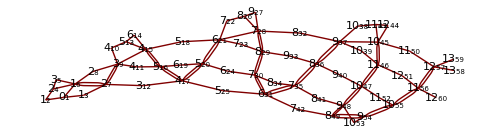

```mathematica
SSSDisplay[UseDistances->True,NetSize->500,NetMax->60,NetMethod->{GraphPlot,NoSSS}]
```

```mathematica
checkDimension/@ MergeIntervals /@ MinRulePositions
```

{{dim,2,4 | 13 | 26 | 43 | 64 | 89 | 118 | 151 | 188 | 229 | 274 | 323 | 376 | 433 | 494 | 559
9 | 13 | 17 | 21 | 25 | 29 | 33 | 37 | 41 | 45 | 49 | 53 | 57 | 61 | 65 | 
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 |  | }}

```mathematica
SSSEvolve[200]
checkDimension @ MergeIntervals @ CommonestHistoryPositions
```

Pseudorepeating

{dim,2,230 | 275 | 324 | 377 | 434 | 495 | 560 | 629 | 702 | 779 | 860 | 945
45 | 49 | 53 | 57 | 61 | 65 | 69 | 73 | 77 | 81 | 85 | 
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 |  | }

```mathematica
SSSEvolve[1300]
```

Pseudorepeating

```mathematica
IdentifyPseudorepeating
```

{{3,{5,∞},5 | 18 | 49 | 106 | 197 | 330 | 513 | 754 | 1061 | 1442
13 | 31 | 57 | 91 | 133 | 183 | 241 | 307 | 381 | 
18 | 26 | 34 | 42 | 50 | 58 | 66 | 74 |  | 
8 | 8 | 8 | 8 | 8 | 8 | 8 |  |  | },{3,{6,∞},6 | 19 | 50 | 107 | 198 | 331 | 514 | 755 | 1062 | 1443
13 | 31 | 57 | 91 | 133 | 183 | 241 | 307 | 381 | 
18 | 26 | 34 | 42 | 50 | 58 | 66 | 74 |  | 
8 | 8 | 8 | 8 | 8 | 8 | 8 |  |  | },{failed,331 | 514 | 755 | 1062 | 1443
183 | 241 | 307 | 381 | 
58 | 66 | 74 |  | ,{1.13793,1.12121}},{3,{5,∞},5 | 17 | 48 | 105 | 196 | 329 | 512 | 753 | 1060 | 1403
12 | 31 | 57 | 91 | 133 | 183 | 241 | 307 | 343 | 
19 | 26 | 34 | 42 | 50 | 58 | 66 | 36 |  | 
7 | 8 | 8 | 8 | 8 | 8 | -30 |  |  | }}

sssSummary: {{3,{5,∞}},{3,{6,∞}},{3,{5,∞}}}

match ({-2,3,1,1,1,1,1,1,1}) with Partition[data,2], starting at 1

distanceTallyAns: {{3,{1,∞},1 | 2 | 5 | 9 | 13 | 16 | 22 | 29 | 40 | 51 | 67 | 82 | 103 | 126 | 156 | 183 | 218 | 257 | 305 | 348 | 401
1 | 3 | 4 | 4 | 3 | 6 | 7 | 11 | 11 | 16 | 15 | 21 | 23 | 30 | 27 | 35 | 39 | 48 | 43 | 53 | 
2 | 1 | 0 | -1 | 3 | 1 | 4 | 0 | 5 | -1 | 6 | 2 | 7 | -3 | 8 | 4 | 9 | -5 | 10 |  | 
-1 | -1 | -1 | 4 | -2 | 3 | -4 | 5 | -6 | 7 | -4 | 5 | -10 | 11 | -4 | 5 | -14 | 15 |  |  | },{failed}}

distanceTallySummary: {3}

{True,{3,{5,∞}}}

```mathematica
toReducedRank@$SSSRuleSet
```

916513216150

```mathematica
toReducedRank@ToCanonical[$SSSRuleSet]
```

792482090026

```mathematica
MaxStateLengthPositions
MergeIntervals@%
checkDimension[%]
```

{3,6,19,50,107,198,331,514}

{6,19,50,107,198,331,514}

{failed,6 | 19 | 50 | 107 | 198 | 331 | 514
13 | 31 | 57 | 91 | 133 | 183 | 
18 | 26 | 34 | 42 | 50 |  | 
8 | 8 | 8 | 8 |  |  | 
0 | 0 | 0 |  |  |  | ,{Indeterminate,Indeterminate}}

```mathematica
SSSEvolve[800]
```

Pseudorepeating

```mathematica
DistanceLastPositions
MergeIntervals[%]
checkDimension@%
```

{2,5,11,17,38,48,91,105,178,196,307,329,486,512,723,753,1026,1060,1403,1441}

{5,17,48,105,196,329,512,753,1060,1403}

{dim,3,5 | 17 | 48 | 105 | 196 | 329 | 512 | 753 | 1060 | 1403
12 | 31 | 57 | 91 | 133 | 183 | 241 | 307 | 343 | 
19 | 26 | 34 | 42 | 50 | 58 | 66 | 36 |  | 
7 | 8 | 8 | 8 | 8 | 8 | -30 |  |  | }

```mathematica
MinRulePositions
MergeIntervals /@ %
checkDimension/@%
```

{{2,5,18,49,106,197,330,513,754,1061,1442}}

{{5,18,49,106,197,330,513,754,1061,1442}}

{{dim,3,5 | 18 | 49 | 106 | 197 | 330 | 513 | 754 | 1061 | 1442
13 | 31 | 57 | 91 | 133 | 183 | 241 | 307 | 381 | 
18 | 26 | 34 | 42 | 50 | 58 | 66 | 74 |  | 
8 | 8 | 8 | 8 | 8 | 8 | 8 |  |  | }}

```mathematica
SSSEvolve[1200]
```

Pseudorepeating

```mathematica
checkDimension@MergeIntervals@CommonestHistoryPositions
```

{dim,3,331 | 514 | 755 | 1062 | 1443 | 1906 | 2459 | 3110
183 | 241 | 307 | 381 | 463 | 553 | 651 | 
58 | 66 | 74 | 82 | 90 | 98 |  | 
8 | 8 | 8 | 8 | 8 |  |  | }

```mathematica
checkDimension[DistanceTally]
```

match ({3,1,1,1,1,1,1,1,1,1,1}) with Partition[data,2], starting at 2

{dim,3,2 | 5 | 9 | 13 | 16 | 22 | 29 | 40 | 51 | 67 | 82 | 103 | 126 | 156 | 183 | 218 | 257 | 305 | 348 | 401 | 460 | 530 | 593 | 668 | 751 | 847
3 | 4 | 4 | 3 | 6 | 7 | 11 | 11 | 16 | 15 | 21 | 23 | 30 | 27 | 35 | 39 | 48 | 43 | 53 | 59 | 70 | 63 | 75 | 83 | 96 | 
1 | 0 | -1 | 3 | 1 | 4 | 0 | 5 | -1 | 6 | 2 | 7 | -3 | 8 | 4 | 9 | -5 | 10 | 6 | 11 | -7 | 12 | 8 | 13 |  | 
-1 | -1 | 4 | -2 | 3 | -4 | 5 | -6 | 7 | -4 | 5 | -10 | 11 | -4 | 5 | -14 | 15 | -4 | 5 | -18 | 19 | -4 | 5 |  |  | }

Length[$SSSEvolution]: 101

```mathematica
SSSEvolve[300]
```

OK

```mathematica
SSSAnimateByDistance
```

```mathematica
?*Distance*
```

```mathematica
IdentifyPseudorepeating
```

match ({-1,8,16,32,64}) with Partition[data,3], starting at 1

match ({7,16,32,64,128}) with Partition[data,2], starting at 1

{{failed,3 | 9 | 14 | 20 | 29 | 33 | 42 | 47 | 56 | 61 | 72 | 76 | 85 | 90 | 101 | 106 | 115 | 120 | 131 | 136 | 145 | 150 | 163 | 167 | 176 | 181 | 192 | 197 | 206 | 211 | 224 | 229 | 238 | 243 | 254 | 259 | 268 | 273 | 286 | 291 | 300 | 305 | 316 | 321 | 330 | 335 | 350 | 354 | 363 | 368 | 379 | 384 | 393 | 398 | 411 | 416 | 425 | 430 | 441 | 446 | 455 | 460 | 475 | 480 | 489 | 494 | 505 | 510 | 519 | 524 | 537 | 542 | 551 | 556 | 567 | 572 | 581 | 586 | 601 | 606 | 615 | 620 | 631 | 636 | 645 | 650 | 663 | 668 | 677 | 682 | 693 | 698 | 707 | 712 | 729 | 733 | 742 | 747 | 758 | 763 | 772 | 777 | 790 | 795 | 804 | 809 | 820 | 825 | 834 | 839 | 854 | 859 | 868 | 873 | 884 | 889 | 898 | 903 | 916 | 921 | 930 | 935 | 946 | 951 | 960 | 965 | 982 | 987 | 993
6 | 5 | 6 | 9 | 4 | 9 | 5 | 9 | 5 | 11 | 4 | 9 | 5 | 11 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 13 | 4 | 9 | 5 | 11 | 5 | 9 | 5 | 13 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 13 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 15 | 4 | 9 | 5 | 11 | 5 | 9 | 5 | 13 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 15 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 13 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 15 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 13 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 17 | 4 | 9 | 5 | 11 | 5 | 9 | 5 | 13 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 15 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 13 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 17 | 5 | 6 | 
-1 | 1 | 3 | -5 | 5 | -4 | 4 | -4 | 6 | -7 | 5 | -4 | 6 | -6 | 4 | -4 | 6 | -6 | 4 | -4 | 8 | -9 | 5 | -4 | 6 | -6 | 4 | -4 | 8 | -8 | 4 | -4 | 6 | -6 | 4 | -4 | 8 | -8 | 4 | -4 | 6 | -6 | 4 | -4 | 10 | -11 | 5 | -4 | 6 | -6 | 4 | -4 | 8 | -8 | 4 | -4 | 6 | -6 | 4 | -4 | 10 | -10 | 4 | -4 | 6 | -6 | 4 | -4 | 8 | -8 | 4 | -4 | 6 | -6 | 4 | -4 | 10 | -10 | 4 | -4 | 6 | -6 | 4 | -4 | 8 | -8 | 4 | -4 | 6 | -6 | 4 | -4 | 12 | -13 | 5 | -4 | 6 | -6 | 4 | -4 | 8 | -8 | 4 | -4 | 6 | -6 | 4 | -4 | 10 | -10 | 4 | -4 | 6 | -6 | 4 | -4 | 8 | -8 | 4 | -4 | 6 | -6 | 4 | -4 | 12 | -12 | 1 |  | ,{-1.,3.,-1.66667,-1.,-0.8,-1.,-1.,-1.5,-1.16667,-0.714286,-0.8,-1.5,-1.,-0.666667,-1.,-1.5,-1.,-0.666667,-1.,-2.,-1.125,-0.555556,-0.8,-1.5,-1.,-0.666667,-1.,-2.,-1.,-0.5,-1.,-1.5,-1.,-0.666667,-1.,-2.,-1.,-0.5,-1.,-1.5,-1.,-0.666667,-1.,-2.5,-1.1,-0.454545,-0.8,-1.5,-1.,-0.666667,-1.,-2.,-1.,-0.5,-1.,-1.5,-1.,-0.666667,-1.,-2.5,-1.,-0.4,-1.,-1.5,-1.,-0.666667,-1.,-2.,-1.,-0.5,-1.,-1.5,-1.,-0.666667,-1.,-2.5,-1.,-0.4,-1.,-1.5,-1.,-0.666667,-1.,-2.,-1.,-0.5,-1.,-1.5,-1.,-0.666667,-1.,-3.,-1.08333,-0.384615,-0.8,-1.5,-1.,-0.666667,-1.,-2.,-1.,-0.5,-1.,-1.5,-1.,-0.666667,-1.,-2.5,-1.,-0.4,-1.,-1.5,-1.,-0.666667,-1.,-2.,-1.,-0.5,-1.,-1.5,-1.,-0.666667,-1.,-3.,-1.,-0.0833333}},{exp,{2,∞},2 | 9 | 14 | 20 | 26 | 39 | 53 | 67 | 96 | 126 | 156 | 217 | 279 | 341 | 466 | 592 | 718 | 971
7 | 5 | 6 | 6 | 13 | 14 | 14 | 29 | 30 | 30 | 61 | 62 | 62 | 125 | 126 | 126 | 253 | 
-2 | 1 | 0 | 7 | 1 | 0 | 15 | 1 | 0 | 31 | 1 | 0 | 63 | 1 | 0 | 127 |  | ,{-8,2,2,2}},{failed,
,{}},{exp,{3,∞},3 | 9 | 16 | 29 | 43 | 72 | 102 | 163 | 225 | 350 | 476 | 729 | 983
6 | 7 | 13 | 14 | 29 | 30 | 61 | 62 | 125 | 126 | 253 | 254 | 
1 | 6 | 1 | 15 | 1 | 31 | 1 | 63 | 1 | 127 | 1 |  | ,{16/7,2,2,2}}}

sssSummary: {{exp,{2,∞}},{exp,{3,∞}}}

distanceTallyAns: {{2,{1,∞},1 | 3 | 5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 68 | 80 | 93 | 107
2 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2, riffling by ,1,: ,{0,1,1,1,1,1,1,1,1,1,1,1,1}}}

distanceTallySummary: {2}

CAUTION: SSS tests and distance tally tests disagree: {{exp,exp},{2}}

{True,2xexp,{{2,∞}}}

```mathematica
SSSAnimateByDistance
```

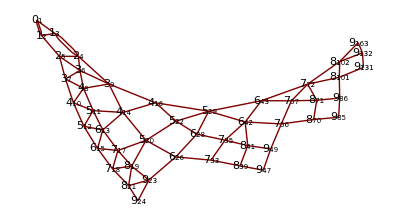

```mathematica
SSSDisplay[UseDistances->True,DistanceMax->9,NetMethod->{NoSSS,GraphPlot}]
```

```mathematica
SSSEvolve[1300]
```

OK

```mathematica
MaxStateLengthPositions
MergeIntervals@%
checkDimension[%]
```

{2,7,9,14,20,26,39,53,67,96,126,156,217,279,341,466,592,718,971,1225,1479,1988}

{2,9,14,20,26,39,53,67,96,126,156,217,279,341,466,592,718,971,1225,1479,1988}

match ({-1,8,16,32,64,128}) with Partition[data,3], starting at 1

{exp,2 | 9 | 14 | 20 | 26 | 39 | 53 | 67 | 96 | 126 | 156 | 217 | 279 | 341 | 466 | 592 | 718 | 971 | 1225 | 1479 | 1988
7 | 5 | 6 | 6 | 13 | 14 | 14 | 29 | 30 | 30 | 61 | 62 | 62 | 125 | 126 | 126 | 253 | 254 | 254 | 509 | 
-2 | 1 | 0 | 7 | 1 | 0 | 15 | 1 | 0 | 31 | 1 | 0 | 63 | 1 | 0 | 127 | 1 | 0 | 255 |  | ,{-8,2,2,2,2}}

```mathematica
DistanceLastPositions
MergeIntervals[%]
checkDimension@%
```

{3,5,9,16,29,43,72,102,163,225,350,476,729,983,1492}

{3,9,16,29,43,72,102,163,225,350,476,729,983,1492}

match ({7,16,32,64,128,256}) with Partition[data,2], starting at 1

{exp,3 | 9 | 16 | 29 | 43 | 72 | 102 | 163 | 225 | 350 | 476 | 729 | 983 | 1492
6 | 7 | 13 | 14 | 29 | 30 | 61 | 62 | 125 | 126 | 253 | 254 | 509 | 
1 | 6 | 1 | 15 | 1 | 31 | 1 | 63 | 1 | 127 | 1 | 255 |  | ,{16/7,2,2,2,2}}

```mathematica
checkDimension[DistanceTally]
```

{dim,2,3 | 5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 68 | 80 | 93 | 107 | 122 | 138 | 155 | 173
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
FindSequenceFunction[DistanceTally,n]
```

1/2 (4+n+n^2)

```mathematica
$SSSRuleUsage
```

{1473,2960,1497}

```mathematica
Length/@MinRulePositions
Length/@ MergeIntervals/@MinRulePositions
```

{1473}

{748}

```mathematica
CommonestHistoryPositions
```

Insufficient data

{}

```mathematica
SSSEvolve[9200]
```

OK

```mathematica
CommonestHistoryPositions
MergeIntervals[%]
checkDimension[%]
```

{277,590,1223,2496,5049}

{277,590,1223,2496,5049}

{failed,277 | 590 | 1223 | 2496 | 5049
313 | 633 | 1273 | 2553 | 
320 | 640 | 1280 |  | ,{2.,2.}}

```mathematica
checkDimension[{277,590,1223,2496,5049,10162}]
```

{exp,2,277,277 | 590 | 1223 | 2496 | 5049 | 10162
313 | 633 | 1273 | 2553 | 5113 | 
320 | 640 | 1280 | 2560 |  | ,{2,2,2}}

This seems to indicate that the SSS exhibits exponential behavior while the network is 2-d and its growing edge is 1-d!  But it certainly looks exponential.

```mathematica
DistanceTally
```

{3,5,8,12,17,23,30,38,47,57,68,80,93,107,122,138,155,173}

```mathematica
Length[DistanceTally]
```

18

```mathematica
testForFractionalExponential
```

Length[$SSSEvolution]: 601

```mathematica
SSSEvolve[500]
```

OK

```mathematica
IdentifyPseudorepeating
```

match ({5,10,20,40,80}) with Partition[data,3], starting at 1

match ({13,20,40,80,160}) with Partition[data,2], starting at 2

{{failed,1 | 4 | 7 | 11 | 14 | 19 | 22 | 27 | 30 | 36 | 39 | 44 | 47 | 54 | 57 | 62 | 65 | 72 | 75 | 80 | 83 | 91 | 94 | 99 | 102 | 109 | 112 | 117 | 120 | 129 | 132 | 137 | 140 | 147 | 150 | 155 | 158 | 167 | 170 | 175 | 178 | 185 | 188 | 193 | 196 | 206 | 209 | 214 | 217 | 224 | 227 | 232 | 235 | 244 | 247 | 252 | 255 | 262 | 265 | 270 | 273 | 284 | 287 | 292 | 295 | 302 | 305 | 310 | 313 | 322 | 325 | 330 | 333 | 340 | 343 | 348 | 351 | 362 | 365 | 370 | 373 | 380 | 383 | 388 | 391 | 400 | 403 | 408 | 411 | 418 | 421 | 426 | 429 | 441 | 444 | 449 | 452 | 459 | 462 | 467 | 470 | 479 | 482 | 487 | 490 | 497 | 500 | 505 | 508 | 519 | 522 | 527 | 530 | 537 | 540 | 545 | 548 | 557 | 560 | 565 | 568 | 575 | 578 | 583 | 586 | 599 | 602 | 607 | 610 | 617 | 620 | 625 | 628 | 637 | 640 | 645 | 648 | 655 | 658 | 663 | 666 | 677 | 680 | 685 | 688 | 695 | 698 | 703 | 706 | 715 | 718 | 723 | 726 | 733 | 736 | 741 | 744 | 757 | 760 | 765 | 768 | 775 | 778 | 783 | 786 | 795 | 798 | 803 | 806 | 813 | 816 | 821 | 824 | 835 | 838 | 843 | 846 | 853 | 856 | 861 | 864 | 873 | 876 | 881 | 884 | 891 | 894 | 899 | 902 | 916 | 919 | 924 | 927 | 934 | 937 | 942 | 945 | 954 | 957 | 962 | 965 | 972 | 975 | 980 | 983 | 994 | 997 | 1002 | 1005 | 1012 | 1015 | 1020 | 1023 | 1032 | 1035 | 1040 | 1043 | 1050 | 1053 | 1058 | 1061 | 1074 | 1077 | 1082 | 1085 | 1092 | 1095 | 1100
3 | 3 | 4 | 3 | 5 | 3 | 5 | 3 | 6 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 8 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 10 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 11 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 11 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 12 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 11 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 13 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 11 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 13 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 11 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 14 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 11 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 13 | 3 | 5 | 3 | 7 | 3 | 5 | ,{1.,1.33333,0.75,1.66667,0.6,1.66667,0.6,2.,0.5,1.66667,0.6,2.33333,0.428571,1.66667,0.6,2.33333,0.428571,1.66667,0.6,2.66667,0.375,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.33333,0.3,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.66667,0.272727,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.66667,0.272727,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,4.,0.25,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.66667,0.272727,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,4.33333,0.230769,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.66667,0.272727,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,4.33333,0.230769,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.66667,0.272727,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,4.66667,0.214286,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.66667,0.272727,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,4.33333,0.230769,1.66667,0.6,2.33333,0.428571,1.66667}},{exp,{2,∞},2 | 5 | 8 | 15 | 23 | 31 | 48 | 66 | 84 | 121 | 159 | 197 | 274 | 352 | 430 | 587 | 745 | 903
3 | 3 | 7 | 8 | 8 | 17 | 18 | 18 | 37 | 38 | 38 | 77 | 78 | 78 | 157 | 158 | 158 | 
0 | 4 | 1 | 0 | 9 | 1 | 0 | 19 | 1 | 0 | 39 | 1 | 0 | 79 | 1 | 0 |  | ,{2,2,2,2}},{failed,
,{}},{exp,{7,∞},4 | 7 | 11 | 18 | 35 | 53 | 90 | 128 | 205 | 283 | 440 | 598 | 915
3 | 4 | 7 | 17 | 18 | 37 | 38 | 77 | 78 | 157 | 158 | 317 | 
1 | 3 | 10 | 1 | 19 | 1 | 39 | 1 | 79 | 1 | 159 |  | ,{20/13,2,2,2}}}

sssSummary: {{exp,{2,∞}},{exp,{7,∞}}}

distanceTallyAns: {{2,{1,∞},1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66 | 78 | 91 | 105
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2, riffling by ,1,: ,{1,1,1,1,1,1,1,1,1,1,1,1}}}

distanceTallySummary: {2}

CAUTION: SSS tests and distance tally tests disagree: {{exp,exp},{2}}

{True,2xexp,{{2,∞}}}

```mathematica
RiffleDistanceTally
```

{2, riffling by ,1,: ,{1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
checkDimension@DistanceTally
```

{2,1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66 | 78 | 91 | 105
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
SSSEvolve[1000]
```

OK

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

match ({5,10,20,40,80,160}) with Partition[data,3], starting at 1

{exp,2 | 5 | 8 | 15 | 23 | 31 | 48 | 66 | 84 | 121 | 159 | 197 | 274 | 352 | 430 | 587 | 745 | 903 | 1220 | 1538
3 | 3 | 7 | 8 | 8 | 17 | 18 | 18 | 37 | 38 | 38 | 77 | 78 | 78 | 157 | 158 | 158 | 317 | 318 | 
0 | 4 | 1 | 0 | 9 | 1 | 0 | 19 | 1 | 0 | 39 | 1 | 0 | 79 | 1 | 0 | 159 | 1 |  | ,{2,2,2,2,2}}

```mathematica
checkDimension@MergeIntervals@DistanceLastPositions
```

match ({4,11,20,40,80,160}) with Partition[data,2], starting at 1

{exp,4 | 7 | 11 | 18 | 35 | 53 | 90 | 128 | 205 | 283 | 440 | 598 | 915 | 1233
3 | 4 | 7 | 17 | 18 | 37 | 38 | 77 | 78 | 157 | 158 | 317 | 318 | 
1 | 3 | 10 | 1 | 19 | 1 | 39 | 1 | 79 | 1 | 159 | 1 |  | ,{11/4,20/11,2,2,2}}

```mathematica
checkDimension@DistanceTally
```

{dim,2,3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66 | 78 | 91 | 105 | 120
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
SSSAnimateByDistance
```

```mathematica
$SSSRuleUsage
```

{639,633,328}

```mathematica
CommonestHistoryPositions
```

Insufficient data

{}

Length[$SSSEvolution]: 801

```mathematica
SSSEvolve[500]
```

OK

```mathematica
IdentifyPseudorepeating
```

match ({6,12,24,48,96}) with Partition[data,3], starting at 1

match ({16,24,48,96,192}) with Partition[data,2], starting at 2

{{failed,4 | 8 | 13 | 19 | 23 | 29 | 33 | 39 | 44 | 50 | 54 | 62 | 66 | 72 | 76 | 84 | 88 | 94 | 98 | 106 | 111 | 117 | 121 | 129 | 133 | 139 | 143 | 153 | 157 | 163 | 167 | 175 | 179 | 185 | 189 | 199 | 203 | 209 | 213 | 221 | 225 | 231 | 235 | 245 | 250 | 256 | 260 | 268 | 272 | 278 | 282 | 292 | 296 | 302 | 306 | 314 | 318 | 324 | 328 | 340 | 344 | 350 | 354 | 362 | 366 | 372 | 376 | 386 | 390 | 396 | 400 | 408 | 412 | 418 | 422 | 434 | 438 | 444 | 448 | 456 | 460 | 466 | 470 | 480 | 484 | 490 | 494 | 502 | 506 | 512 | 516 | 528 | 533 | 539 | 543 | 551 | 555 | 561 | 565 | 575 | 579 | 585 | 589 | 597 | 601 | 607 | 611 | 623 | 627 | 633 | 637 | 645 | 649 | 655 | 659 | 669 | 673 | 679 | 683 | 691 | 695 | 701 | 705 | 719 | 723 | 729 | 733 | 741 | 745 | 751 | 755 | 765 | 769 | 775 | 779 | 787 | 791 | 797 | 801 | 813 | 817 | 823 | 827 | 835 | 839 | 845 | 849 | 859 | 863 | 869 | 873 | 881 | 885 | 891 | 895 | 909 | 913 | 919 | 923 | 931 | 935 | 941 | 945 | 955 | 959 | 965 | 969 | 977 | 981 | 987 | 991 | 1003 | 1007 | 1013 | 1017 | 1025 | 1029 | 1035 | 1039 | 1049 | 1053 | 1059 | 1063 | 1071 | 1075 | 1081 | 1085 | 1099 | 1104 | 1110 | 1114 | 1122 | 1126 | 1132 | 1136 | 1146 | 1150 | 1156 | 1160 | 1168 | 1172 | 1178 | 1182 | 1194 | 1198 | 1204 | 1208 | 1216 | 1220 | 1226 | 1230 | 1240 | 1244 | 1250 | 1254 | 1262 | 1266 | 1272 | 1276 | 1290 | 1294 | 1298
4 | 5 | 6 | 4 | 6 | 4 | 6 | 5 | 6 | 4 | 8 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 8 | 5 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 5 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 12 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 12 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 12 | 5 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 12 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 14 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 12 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 14 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 12 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 14 | 5 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 12 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 14 | 4 | 4 | ,{1.25,1.2,0.666667,1.5,0.666667,1.5,0.833333,1.2,0.666667,2.,0.5,1.5,0.666667,2.,0.5,1.5,0.666667,2.,0.625,1.2,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.5,1.2,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.,0.333333,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.,0.333333,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.,0.416667,1.2,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.,0.333333,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.5,0.285714,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.,0.333333,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.5,0.285714,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.,0.333333,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.5,0.357143,1.2,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.,0.333333,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.5,0.285714,1.}},{exp,{3,∞},3 | 7 | 16 | 26 | 36 | 57 | 79 | 101 | 146 | 192 | 238 | 331 | 425 | 519 | 708 | 898 | 1088
4 | 9 | 10 | 10 | 21 | 22 | 22 | 45 | 46 | 46 | 93 | 94 | 94 | 189 | 190 | 190 | 
5 | 1 | 0 | 11 | 1 | 0 | 23 | 1 | 0 | 47 | 1 | 0 | 95 | 1 | 0 |  | ,{2,2,2,2}},{failed,
,{}},{exp,{7,∞},3 | 7 | 12 | 19 | 40 | 62 | 107 | 153 | 246 | 340 | 529 | 719 | 1100
4 | 5 | 7 | 21 | 22 | 45 | 46 | 93 | 94 | 189 | 190 | 381 | 
1 | 2 | 14 | 1 | 23 | 1 | 47 | 1 | 95 | 1 | 191 |  | ,{3/2,2,2,2}}}

sssSummary: {{exp,{3,∞}},{exp,{7,∞}}}

distanceTallyAns: {{2,{1,∞},1 | 3 | 5 | 9 | 15 | 22 | 30 | 39 | 49 | 60 | 72 | 85 | 99 | 114
2 | 2 | 4 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 
0 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2, riffling by ,1,: ,{0,2,2,1,1,1,1,1,1,1,1,1}}}

distanceTallySummary: {2}

CAUTION: SSS tests and distance tally tests disagree: {{exp,exp},{2}}

{True,2xexp,{{3,∞}}}

```mathematica
SSSEvolve[500]
```

OK

```mathematica
MaxStateLengthPositions
MergeIntervals@%
checkDimension[%]
```

{2,3,7,16,26,36,57,79,101,146,192,238,331,425,519,708,898,1088,1469}

{3,7,16,26,36,57,79,101,146,192,238,331,425,519,708,898,1088,1469}

match ({6,12,24,48,96}) with Partition[data,3], starting at 1

{exp,3 | 7 | 16 | 26 | 36 | 57 | 79 | 101 | 146 | 192 | 238 | 331 | 425 | 519 | 708 | 898 | 1088 | 1469
4 | 9 | 10 | 10 | 21 | 22 | 22 | 45 | 46 | 46 | 93 | 94 | 94 | 189 | 190 | 190 | 381 | 
5 | 1 | 0 | 11 | 1 | 0 | 23 | 1 | 0 | 47 | 1 | 0 | 95 | 1 | 0 | 191 |  | ,{2,2,2,2}}

```mathematica
checkDimension@MergeIntervals@DistanceLastPositions
```

match ({3,15,24,48,96,192}) with Partition[data,2], starting at 1

{exp,3 | 7 | 12 | 19 | 40 | 62 | 107 | 153 | 246 | 340 | 529 | 719 | 1100 | 1482
4 | 5 | 7 | 21 | 22 | 45 | 46 | 93 | 94 | 189 | 190 | 381 | 382 | 
1 | 2 | 14 | 1 | 23 | 1 | 47 | 1 | 95 | 1 | 191 | 1 |  | ,{5,8/5,2,2,2}}

```mathematica
checkDimension@DistanceTally
```

{dim,2,3 | 5 | 9 | 15 | 22 | 30 | 39 | 49 | 60 | 72 | 85 | 99 | 114 | 130
2 | 4 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 
2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
$SSSRuleUsage
```

{596,590,614}

```mathematica
CommonestHistoryPositions
MergeIntervals[%]
checkDimension[%]
```

Insufficient data

{}

{}

{failed,
,{}}

```mathematica
checkDimension@{238,519,1088,2233,4530,9131}
```

{exp,2,238,238 | 519 | 1088 | 2233 | 4530 | 9131
281 | 569 | 1145 | 2297 | 4601 | 
288 | 576 | 1152 | 2304 |  | ,{2,2,2}}

OK

```mathematica
SSSEvolve[1000]
```

OK

```mathematica
SSSEvolve[4000]
```

OK

```mathematica
IdentifyPseudorepeating
```

No successful SSS tests

{True,2}

```mathematica
SSSEvolve[1000]
```

OK

```mathematica
SSSEvolve[1000]
IdentifyPseudorepeating
```

```mathematica
SSSEvolve[1000]
IdentifyPseudorepeating
```

```mathematica
SSSEvolve[1000]
IdentifyPseudorepeating
```

```mathematica
SSSEvolve[1000]
IdentifyPseudorepeating
```

```mathematica
Length[$SSSEvolution]
```

15000

```mathematica
SSSEvolve[1899]
Length[$SSSEvolution]
IdentifyPseudorepeating
```

OK

13000

```mathematica
SSSEvolve[1899]
Length[$SSSEvolution]
IdentifyPseudorepeating
```

OK

14899

```mathematica
SSSEvolve[101]
Length[$SSSEvolution]
IdentifyPseudorepeating
```

OK

15000

```mathematica
SSSEvolve[1000]
Length[$SSSEvolution]
IdentifyPseudorepeating
```

OK

20000

No successful SSS tests

{True,2qq}

```mathematica
RiffleDistanceTally
```

{2, riffling by ,2,: ,{3,3,4,4,4,4,4,4}}

```mathematica
IdentifyPseudorepeating
```

No successful SSS tests

{True,2qq}

```mathematica
Differences[DistanceTally]
```

{3,4,6,7,10,11,14,15,18,19}

```mathematica
Differences[DistanceTally,1,2]
```

{7,10,13,17,21,25,29,33,37}

```mathematica
MaxStateLengthPositions
MergeIntervals[%]
checkDimension[%]
```

{2,3,8,9,17,19,24,44,49,54,55,93,133,195,197,265,291,356,406,408,557,676,770,1012,1281,1487,1492,1493,2949,4037,4039,5583,7318,7719,7720,13569,14603}

{9,24,93,197,557,1012,2949,5583,7318}

{failed,9 | 24 | 93 | 197 | 557 | 1012 | 2949 | 5583 | 7318
15 | 69 | 104 | 360 | 455 | 1937 | 2634 | 1735 | 
54 | 35 | 256 | 95 | 1482 | 697 | -899 |  | 
-19 | 221 | -161 | 1387 | -785 | -1596 |  |  | 
240 | -382 | 1548 | -2172 | -811 |  |  |  | 
-622 | 1930 | -3720 | 1361 |  |  |  |  | 
2552 | -5650 | 5081 |  |  |  |  |  | ,{-2.21395,-0.899292}}

```mathematica
Grid[Table[{Mean[#],StandardDeviation[#]}&@N@Differences[MergeIntervals@MaxStateLengthPositions,n],{n,0,6}]]
```

1971.33 | 2734.66
913.625 | 1026.43
245.714 | 724.156
-158.833 | 1001.1
-315.4 | 1367.27
-262.75 | 2551.23
661. | 5609.86

```mathematica
Grid[Table[LinearModelFit[Differences[MergeIntervals@MaxStateLengthPositions,n],x,x][#]&/@{"BestFit","RSquared"},{n,0,6}]]
```

-2398.67+874. x | 0.766088
-718.107+362.607 x | 0.748801
289.857-11.0357 x | 0.00108379
776.667-267.286 x | 0.249499
852.2-389.2 x | 0.20257
-337.5+29.9 x | 0.000228924
-1868.+1264.5 x | 0.0508082

```mathematica
Grid[Table[N@Ratios@Differences[MergeIntervals[MaxStateLengthPositions],n],{n,0,6}]]
```

2.66667 | 3.875 | 2.11828 | 2.82741 | 1.81688 | 2.91403 | 1.89318 | 1.31076
4.6 | 1.50725 | 3.46154 | 1.26389 | 4.25714 | 1.35983 | 0.658694 | 
0.648148 | 7.31429 | 0.371094 | 15.6 | 0.47031 | -1.28981 |  | 
-11.6316 | -0.728507 | -8.61491 | -0.56597 | 2.03312 |  |  | 
-1.59167 | -4.05236 | -1.4031 | 0.373389 |  |  |  | 
-3.10289 | -1.92746 | -0.36586 |  |  |  |  | 
-2.21395 | -0.899292 |  |  |  |  |  |

```mathematica
Grid[Table[{Mean[#],StandardDeviation[#]}&@N@Ratios@Differences[MergeIntervals@MaxStateLengthPositions,n],{n,0,6}]]
```

2.42778 | 0.806241
2.44405 | 1.61266
3.85234 | 6.48473
-3.90157 | 5.88183
-1.66843 | 1.8192
-1.79874 | 1.37305
-1.55662 | 0.929603

```mathematica
Grid[Table[LinearModelFit[N@Ratios@Differences[MergeIntervals@MaxStateLengthPositions,n],x,x][#]&/@{"BestFit","RSquared"},{n,0,6}]]
```

3.39333-0.214568 x | 0.424962
4.06164-0.404398 x | 0.293452
5.35162-0.428367 x | 0.0152727
-12.1491+2.74919 x | 0.546167
-3.80454+0.854442 x | 0.367667
-4.53577+1.36852 x | 0.993408
-3.52861+1.31466 x | 1.

```mathematica
DistanceLastPositions
MergeIntervals[%]
checkDimension@%
```

{6,10,28,66,205,417,1110,2200,5734,11260}

{10,28,66,205,417,1110,2200,5734,11260}

{failed,10 | 28 | 66 | 205 | 417 | 1110 | 2200 | 5734 | 11260
18 | 38 | 139 | 212 | 693 | 1090 | 3534 | 5526 | 
20 | 101 | 73 | 481 | 397 | 2444 | 1992 |  | 
81 | -28 | 408 | -84 | 2047 | -452 |  |  | 
-109 | 436 | -492 | 2131 | -2499 |  |  |  | 
545 | -928 | 2623 | -4630 |  |  |  |  | 
-1473 | 3551 | -7253 |  |  |  |  |  | ,{-2.41073,-2.04252}}

```mathematica
Grid[Table[{Mean[#],StandardDeviation[#]}&@N@Differences[MergeIntervals@DistanceLastPositions,n],{n,0,6}]]
```

2336.67 | 3821.31
1406.25 | 2033.29
786.857 | 1001.01
328.667 | 886.256
-106.6 | 1671.33
-597.5 | 3057.63
-1725. | 5406.41

```mathematica
Differences[Differences[MergeIntervals@DistanceLastPositions,3],1,2]
```

{327,-56,1639,-368}

```mathematica
Grid[Table[LinearModelFit[Differences[MergeIntervals@DistanceLastPositions,n],x,x][#]&/@{"BestFit","RSquared"},{n,0,6}]]
```

-3270.92+1121.52 x | 0.646022
-1774.29+706.786 x | 0.724983
-774.+390.214 x | 0.709151
21.8667+87.6571 x | 0.0342393
818.9-308.5 x | 0.0851776
2396.-1197.4 x | 0.255599
4055.-2890. x | 0.285745

```mathematica
Grid[Table[N@Ratios@Differences[MergeIntervals[DistanceLastPositions],n],{n,0,6}]]
```

2.8 | 2.35714 | 3.10606 | 2.03415 | 2.66187 | 1.98198 | 2.60636 | 1.96373
2.11111 | 3.65789 | 1.52518 | 3.26887 | 1.57287 | 3.2422 | 1.56367 | 
5.05 | 0.722772 | 6.58904 | 0.825364 | 6.15617 | 0.815057 |  | 
-0.345679 | -14.5714 | -0.205882 | -24.369 | -0.220811 |  |  | 
-4. | -1.12844 | -4.3313 | -1.17269 |  |  |  | 
-1.70275 | -2.82651 | -1.76515 |  |  |  |  | 
-2.41073 | -2.04252 |  |  |  |  |  |

```mathematica
Grid[Table[{Mean[#],StandardDeviation[#]}&@N@Ratios@Differences[MergeIntervals@DistanceLastPositions,n],{n,0,6}]]
```

2.43891 | 0.423983
2.42026 | 0.93773
3.35973 | 2.86208
-7.94257 | 11.0789
-2.65811 | 1.7461
-2.09814 | 0.631558
-2.22662 | 0.260359

```mathematica
Mean[{2.43891,2.42026,3.35973}]
```

2.73963

```mathematica
Grid[Table[LinearModelFit[N@Ratios@Differences[MergeIntervals@DistanceLastPositions,n],x,x][#]&/@{"BestFit","RSquared"},{n,0,6}]]
```

2.83279-0.0875278 x | 0.255709
2.76683-0.0866438 x | 0.0398406
4.42355-0.303948 x | 0.0394734
-5.0782-0.954788 x | 0.0185679
-3.97788+0.527907 x | 0.152344
-2.03574-0.0312011 x | 0.00244068
-2.77893+0.368203 x | 1.

```mathematica
checkDimension@DistanceTally
```

{failed,1 | 4 | 8 | 14 | 21 | 31 | 42 | 56 | 71 | 89 | 108
3 | 4 | 6 | 7 | 10 | 11 | 14 | 15 | 18 | 19 | 
1 | 2 | 1 | 3 | 1 | 3 | 1 | 3 | 1 |  | 
1 | -1 | 2 | -2 | 2 | -2 | 2 | -2 |  |  | 
-2 | 3 | -4 | 4 | -4 | 4 | -4 |  |  |  | 
5 | -7 | 8 | -8 | 8 | -8 |  |  |  |  | 
-12 | 15 | -16 | 16 | -16 |  |  |  |  |  | 
27 | -31 | 32 | -32 |  |  |  |  |  |  | 
-58 | 63 | -64 |  |  |  |  |  |  |  | ,{-1.08621,-1.01587}}

```mathematica
Grid[Table[{Mean[#],StandardDeviation[#]}&@N@Differences[DistanceTally,n],{n,0,5}]]
```

33.7 | 30.1553
9.77778 | 5.1908
1.875 | 0.991031
0.285714 | 1.88982
0.166667 | 3.92003
1.2 | 8.04363

```mathematica
Grid[Table[LinearModelFit[Differences[DistanceTally,n],x,x][#]&/@{"BestFit","RSquared"},{n,0,6}]]
```

-23.3091+10.6273 x | 0.940963
0.4+1.87273 x | 0.990539
1.52778+0.05 x | 0.0198529
0.75-0.166667 x | 0.0448718
0.142857-0.142857 x | 0.00623053
3.26667-1.02857 x | 0.0562175
-0.5-0.7 x | 0.00444162

```mathematica
Grid[Table[N@Ratios@Differences[DistanceTally,n],{n,0,3}]]
```

4. | 2. | 1.75 | 1.5 | 1.47619 | 1.35484 | 1.33333 | 1.26786 | 1.25352
1.33333 | 1.5 | 1.16667 | 1.42857 | 1.1 | 1.27273 | 1.07143 | 1.2 | 
2. | 0.5 | 3. | 0.333333 | 3. | 0.333333 | 3. |  | 
-1. | -2. | -1. | -1. | -1. | -1. |  |  |

```mathematica
Grid[Table[{Mean[#],StandardDeviation[#]}&@N@Ratios@Differences[DistanceTally,n],{n,0,2}]]
```

1.77064 | 0.870873
1.25909 | 0.153539
1.7381 | 1.31183

```mathematica
Grid[Table[LinearModelFit[N@Ratios@Differences[DistanceTally,n],x,x][#]&/@{"BestFit","RSquared"},{n,0,2}]]
```

2.95071-0.236014 x | 0.550842
1.42444-0.036745 x | 0.343645
1.35714+0.0952381 x | 0.0245965

```mathematica
RiffleDistanceTally
```

dim riffling by 2: {3,3,4,4,4,4,4}

```mathematica
Grid[{Range[1,9],Differences[DistanceTally]}]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
3 | 4 | 6 | 7 | 10 | 11 | 14 | 15 | 18

```mathematica
$SSSRuleUsage
```

{6048,8,3044}

```mathematica
checkDimension/@ MergeIntervals /@ MinRulePositions
```

{{failed,11 | 28 | 99 | 205 | 567 | 1110 | 2963 | 5734
17 | 71 | 106 | 362 | 543 | 1853 | 2771 | 
54 | 35 | 256 | 181 | 1310 | 918 |  | 
-19 | 221 | -75 | 1129 | -392 |  |  | 
240 | -296 | 1204 | -1521 |  |  |  | 
-536 | 1500 | -2725 |  |  |  |  | ,{-2.79851,-1.81667}}}

```mathematica
MergeIntervals /@ MinRulePositions
```

{{11,28,99,205,567,1110,2963,5734}}

```mathematica
Grid[Table[N@Ratios@Differences[First[MinRulePositions],n],{n,0,4}]]
```

2.54545 | 3.53571 | 2.07071 | 2.76585 | 1.95767 | 2.66937 | 1.9352
4.17647 | 1.49296 | 3.41509 | 1.5 | 3.41252 | 1.49541 | 
0.648148 | 7.31429 | 0.707031 | 7.23757 | 0.700763 |  | 
-11.6316 | -0.339367 | -15.0533 | -0.34721 |  |  | 
-1.23333 | -4.06757 | -1.26329 |  |  |  |

```mathematica
Grid[Table[{Mean[#],StandardDeviation[#]}&@N@Ratios@Differences[First[MinRulePositions],n],{n,0,6}]]
```

StandardDeviation::shlen: The argument {-2.07515} should have at least two elements.

2.49714 | 0.57322
2.58208 | 1.22177
3.32156 | 3.61
-6.84287 | 7.63397
-2.18806 | 1.62777
-2.30759 | 0.694266
-2.07515 | StandardDeviation[{-2.07515}]

Just taking ratios, we see that the first row wavers around 2 or 2.5, sounds like exponential growth, although it doesn’t stabilize and in fact the fluctuation becomes worse in successive rows.  Try clumping by twos to adjust for fluctuation:

```mathematica
Grid[Table[N@Ratios@Differences[Total/@Partition[First[MinRulePositions],2],n],{n,0,2}]]
```

7.79487 | 5.51645 | 5.18605
5.18113 | 5.11289 | 
5.09657 |  |

Or just skip every other one before forming ratos of repeated differences:

```mathematica
Last/@Partition[First[MinRulePositions],2]
```

{28,205,1110,5734}

```mathematica
Grid[Table[N@Ratios@Differences[Last/@Partition[First[MinRulePositions],2],n],{n,0,2}]]
```

7.32143 | 5.41463 | 5.16577
5.11299 | 5.10939 | 
5.10852 |  |

Either way, it’s very tempting to call this exponential dimension 5.10/2=2.55.

```mathematica
CommonestHistoryPositions
MergeIntervals[%]
checkDimension[%]
```

Insufficient data

{}

{}

{failed,
,{}}

```mathematica
MaxStateLengthPositions
MergeIntervals@%
checkDimension[%]
```

{2,3,4,5,18,31,32,33,37,38,43,44,48,49,60,61,62,65,66,85,86,101,102,103,140,141,146,155,156,157,186,187,192,245,246,251,406,407,408,409,410,411,416,539,540,545,702,841,842,847,988,993,1132,1133,1138,1285,1286,1291,1428,1429,1430,1435,1590,1595,1746,1747,1752,1925,1930,2079,2080,2081,2086,2251,2256,2449,2450,2455,2750,2751,2752,2753,2754,2755,2760,3023,3024,3029,3326,3605,3606,3611,3892,3897,4176,4177,4182,4469,4470,4475,4752,4753,4754,4759,5054,5059,5350,5351,5356,5669,5674,5963,5964,5965,5970,6275,6280,6613,6614,6619,7054,7055,7056,7057,7058,7059,7064}

{5,18,33,38,44,49,62,66,86,103,146,157,192,251,416,545,702,847,993,1138,1291,1435,1595,1752,1930,2086,2256,2455,2760,3029,3326,3611,3897,4182,4475,4759,5059,5356,5674,5970,6280,6619,7059}

```mathematica
DistanceLastPositions
MergeIntervals[%]
checkDimension@%
```

{9,14,29,391,679,2721,3289,7011}

{14,29,391,679,2721,3289,7011}

{failed,14 | 29 | 391 | 679 | 2721 | 3289 | 7011
15 | 362 | 288 | 2042 | 568 | 3722 | 
347 | -74 | 1754 | -1474 | 3154 |  | 
-421 | 1828 | -3228 | 4628 |  |  | 
2249 | -5056 | 7856 |  |  |  | ,{-2.24811,-1.5538}}

```mathematica
checkDimension@DistanceTally
```

{failed,1 | 4 | 9 | 16 | 25 | 38 | 55 | 78 | 111
3 | 5 | 7 | 9 | 13 | 17 | 23 | 33 | 
2 | 2 | 2 | 4 | 4 | 6 | 10 |  | 
0 | 0 | 2 | 0 | 2 | 4 |  |  | 
0 | 2 | -2 | 2 | 2 |  |  |  | 
2 | -4 | 4 | 0 |  |  |  |  | 
-6 | 8 | -4 |  |  |  |  |  | ,{-1.33333,-0.5}}

```mathematica
RiffleDistanceTally
```

{failed}

```mathematica
$SSSRuleUsage
```

{3526,3529,45}

```mathematica
MinRulePositions
MergeIntervals /@ %
checkDimension/@%
```

{{1,3,4,16,30,36,42,47,59,64,82,99,136,153,182,239,396,525,680,826,972,1117,1269,1414,1572,1729,1906,2063,2232,2429,2726,2995,3290,3576,3862,4147,4439,4724,5022,5319,5636,5933,6242,6579,7016,7425,7860,8286,8712}}

{{4,16,30,36,42,47,59,64,82,99,136,153,182,239,396,525,680,826,972,1117,1269,1414,1572,1729,1906,2063,2232,2429,2726,2995,3290,3576,3862,4147,4439,4724,5022,5319,5636,5933,6242,6579,7016,7425,7860,8286,8712}}

```mathematica
CommonestHistoryPositions
```

{1729,1906,2063,2232,2429,5319,5636,5933,6242,6579}

```mathematica
MergeIntervals[%]
checkDimension[%]
```

{1729,1906,2063,2232,2429,5319,5636,5933,6242,6579}

{failed,1729 | 1906 | 2063 | 2232 | 2429 | 5319 | 5636 | 5933 | 6242 | 6579
177 | 157 | 169 | 197 | 2890 | 317 | 297 | 309 | 337 | 
-20 | 12 | 28 | 2693 | -2573 | -20 | 12 | 28 |  | 
32 | 16 | 2665 | -5266 | 2553 | 32 | 16 |  |  | 
-16 | 2649 | -7931 | 7819 | -2521 | -16 |  |  |  | 
2665 | -10580 | 15750 | -10340 | 2505 |  |  |  |  | 
-13245 | 26330 | -26090 | 12845 |  |  |  |  |  | ,{-1.98792,-0.990885,-0.492334}}